# Quintic splines

```mathematica
ClearAll["Global`*"]
```

### Basis functions

Determine the basis functions by solving the appropriate linear system:

```mathematica
poly[x_]=Sum[Subscript[a, i] x^i,{i,0,5}]
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5

```mathematica
coef=CoefficientList[poly[x],x]
```

{a_0,a_1,a_2,a_3,a_4,a_5}

```mathematica
h00[x_]=poly[x]/.First[Solve[{poly[0]==1,poly[1]==0,poly'[0]==0,poly'[1]==0,poly''[0]==0,poly''[1]==0},coef]];
```

```mathematica
h01[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==1,poly'[0]==0,poly'[1]==0,poly''[0]==0,poly''[1]==0},coef]];
```

```mathematica
h10[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==0,poly'[0]==1,poly'[1]==0,poly''[0]==0,poly''[1]==0},coef]];
```

```mathematica
h11[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==0,poly'[0]==0,poly'[1]==1,poly''[0]==0,poly''[1]==0},coef]];
```

```mathematica
h20[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==0,poly'[0]==0,poly'[1]==0,poly''[0]==1,poly''[1]==0},coef]];
```

```mathematica
h21[x_]=poly[x]/.First[Solve[{poly[0]==0,poly[1]==0,poly'[0]==0,poly'[1]==0,poly''[0]==0,poly''[1]==1},coef]];
```

Expressions of the basis functions:

```mathematica
TableForm[Map[#&,{h00[x],h01[x],h10[x],h11[x],h20[x],h11[x]}],TableHeadings->{{"h00","h01","h10","h11","h20","h21"}}]
```

h00 | 1-10 x^3+15 x^4-6 x^5
h01 | 10 x^3-15 x^4+6 x^5
h10 | x-6 x^3+8 x^4-3 x^5
h11 | -4 x^3+7 x^4-3 x^5
h20 | x^2/2-(3 x^3)/2+(3 x^4)/2-x^5/2
h21 | -4 x^3+7 x^4-3 x^5

Their first derivatives:

```mathematica
TableForm[Map[D[#,x]&,{h00[x],h01[x],h10[x],h11[x],h20[x],h11[x]}],TableHeadings->{{"h00","h01","h10","h11","h20","h21"}}]
```

h00 | -30 x^2+60 x^3-30 x^4
h01 | 30 x^2-60 x^3+30 x^4
h10 | 1-18 x^2+32 x^3-15 x^4
h11 | -12 x^2+28 x^3-15 x^4
h20 | x-(9 x^2)/2+6 x^3-(5 x^4)/2
h21 | -12 x^2+28 x^3-15 x^4

Their second derivatives:

```mathematica
TableForm[Map[D[#,{x,2}]&,{h00[x],h01[x],h10[x],h11[x],h20[x],h11[x]}],TableHeadings->{{"h00","h01","h10","h11","h20","h21"}}]
```

h00 | -60 x+180 x^2-120 x^3
h01 | 60 x-180 x^2+120 x^3
h10 | -36 x+96 x^2-60 x^3
h11 | -24 x+84 x^2-60 x^3
h20 | 1-9 x+18 x^2-10 x^3
h21 | -24 x+84 x^2-60 x^3

Their fourth derivatives:

```mathematica
TableForm[Map[D[#,{x,4}]&,{h00[x],h01[x],h10[x],h11[x],h20[x],h11[x]}],TableHeadings->{{"h00","h01","h10","h11","h20","h21"}}]
```

h00 | 360-720 x
h01 | -360+720 x
h10 | 192-360 x
h11 | 168-360 x
h20 | 36-60 x
h21 | 168-360 x

Plots of the basis functions:

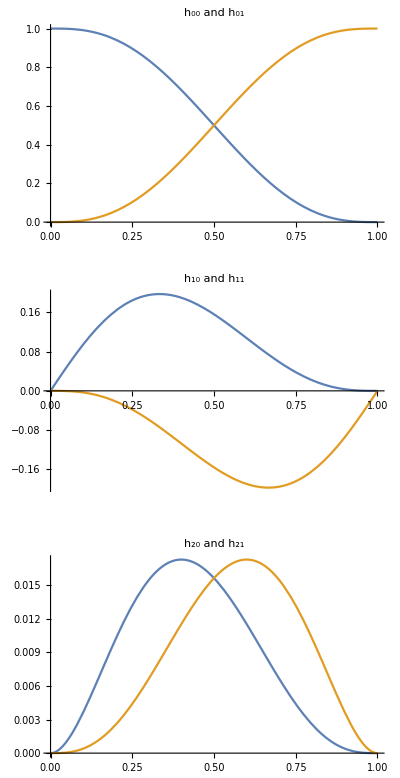

```mathematica
GraphicsColumn[{Plot[{h00[x],h01[x]},{x,0,1},PlotLabel->"h_00 and h_01"],Plot[{h10[x],h11[x]},{x,0,1},PlotLabel->"h_10 and h_11"],Plot[{h20[x],h21[x]},{x,0,1},PlotLabel->"h_20 and h_21"]}]
```

Their first derivatives:

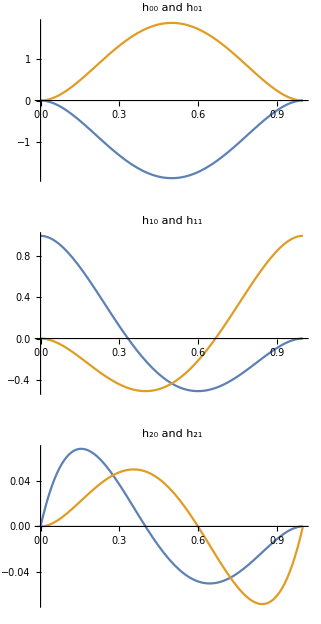

```mathematica
GraphicsColumn[{Plot[Evaluate[{h00'[x],h01'[x]}],{x,0,1},PlotLabel->"h_00 and h_01"],Plot[Evaluate[{h10'[x],h11'[x]}],{x,0,1},PlotLabel->"h_10 and h_11"],Plot[Evaluate[{h20'[x],h21'[x]}],{x,0,1},PlotLabel->"h_20 and h_21"]}]
```

Their second derivatives:

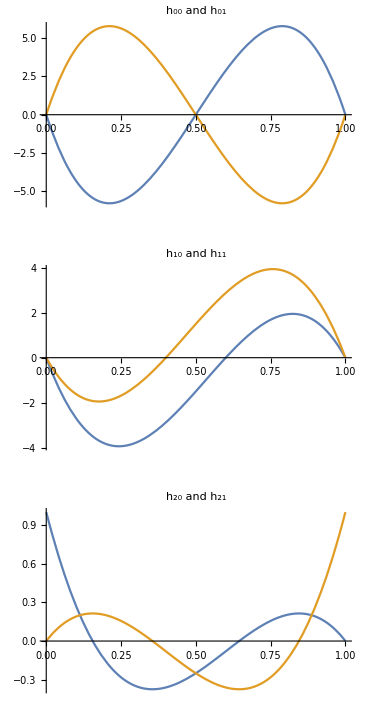

```mathematica
GraphicsColumn[{Plot[Evaluate[{h00''[x],h01''[x]}],{x,0,1},PlotLabel->"h_00 and h_01"],Plot[Evaluate[{h10''[x],h11''[x]}],{x,0,1},PlotLabel->"h_10 and h_11"],Plot[Evaluate[{h20''[x],h21''[x]}],{x,0,1},PlotLabel->"h_20 and h_21"]}]
```

### Interpolation function

The interpolating function over [0, 1] is a linear combination of those six basis functions:

```mathematica
h[x_,y0_,y1_,s0_,s1_,a0_,a1_]=y0*h00[x]+y1*h01[x]+s0*h10[x]+s1*h11[x]+a0*h20[x]+a1*h21[x];
```

```mathematica
Manipulate[GraphicsColumn[{Plot[h[x,y0,y1,s0,s1,a0,a1],{x,0,1},PlotRange->{{0,1},{-2,2}},PlotLabel->"Quintic spline function"],Plot[Evaluate[D[h[x,y0,y1,s0,s1,a0,a1],x]],{x,0,1},PlotRange->{{0,1},{-10,10}},PlotLabel->"First derivative"],Plot[Evaluate[D[h[x,y0,y1,s0,s1,a0,a1],{x,2}]],{x,0,1},PlotRange->{{0,1},{-50,50}},PlotLabel->"Second derivative"]}],{{y0,-1},-2,2},{{y1,1},-2,2},{{s0,0},-2,2},{{s1,0},-2,2},{{a0,0},-20,20},{{a1,0},-20,20}]
```

We can extend this function to an arbitrary interval using an affine transformation:

```mathematica
f[x_]=y0*h00[(x-x0)/(x1-x0)]+y1*h01[(x-x0)/(x1-x0)]+s0*(x1-x0)*h10[(x-x0)/(x1-x0)]+s1*(x1-x0)*h11[(x-x0)/(x1-x0)]+a0*(x1-x0)^2*h20[(x-x0)/(x1-x0)]+a1*(x1-x0)^2*h21[(x-x0)/(x1-x0)];
```

Check that the function and its derivatives have the right values:

```mathematica
f[x0]
```

y0

```mathematica
f[x1]
```

y1

```mathematica
f'[x0]
```

s0

```mathematica
f'[x1]
```

s1

```mathematica
f''[x0]
```

a0

```mathematica
f''[x1]
```

a1

### Constraint on the spline

The interpolation method requires certain conditions on the spline to get a nondecreasing quantile function. We search for a lower bound of the polynomial h''(x)+h'(x)(x_1-x_0-h'(x)).

```mathematica
g=D[h[x,y0,y1,s0,s1,a0,a1],{x,2}]+D[h[x,y0,y1,s0,s1,a0,a1],x]*(x1-x0-D[h[x,y0,y1,s0,s1,a0,a1],x]);
```

```mathematica
gcoefs=Simplify[CoefficientList[g,x]];
```

We rewrite the polynomial in its Bernstein form:

```mathematica
tobernstein[k_]:=Sum[Part[gcoefs,r+1]*Binomial[k,r]/Binomial[Length[gcoefs]-1,r],{r,0,k}]
```

```mathematica
bernsteincoefs=FullSimplify[Map[tobernstein,Range[0,Length[gcoefs]-1]]];
```

Hence, we require all the following expressions to be non-negative:

```mathematica
TableForm[bernsteincoefs]
```

a0-s0 (s0+x0-x1)
a0-s0 (s0+x0-x1)+1/8 (-a0 (9+2 s0+x0-x1)+3 (a1-4 (3 s0+2 s1+5 y0-5 y1)))
1/56 (-2 a0^2-a0 (34+10 s0+5 x0-5 x1)+3 a1 (6-2 s0-x0+x1)+4 (4 s0^2+3 (2 s1 (-7+x0-x1)+5 (-8+x0-x1) (y0-y1))+s0 (-78+12 s1-5 x0+5 x1+30 y0-30 y1)))
1/56 (3 a0^2+a1-5 a1 (2 s0+x0-x1)+4 (24 s0^2+(x0-x1) (11 s1+30 (y0-y1))+s0 (22 s1+5 x0-5 x1+60 y0-60 y1))+a0 (-35-3 a1+36 s0+24 s1+60 y0-60 y1)-60 (4 s0+s1+5 y0-5 y1))
1/280 (-9 a0^2-9 a1^2+2 a0 (13 a1-2 (25+36 s0+44 s1-5 x0+5 x1+90 y0-90 y1))+4 a1 (44 s0+36 s1-5 (5+x0-x1-18 y0+18 y1))-4 (144 s0^2+144 s1^2+s0 (322 s1-55 x0+55 x1+120 (1+6 y0-6 y1))+180 (-x0+x1+5 y0-5 y1) (y0-y1)-5 s1 (11 x0-11 x1+24 (1-6 y0+6 y1))))
1/56 (3 a1^2+a0 (1-3 a1+10 s1+5 x0-5 x1)+4 (24 s1^2+s0 (15+22 s1+11 x0-11 x1)+5 s1 (x0-x1+12 (1+y0-y1))+15 (5+2 x0-2 x1) (y0-y1))-a1 (35+24 s0+36 s1+60 y0-60 y1))
1/56 (-2 a1^2+a1 (-34+10 s1+5 x0-5 x1)+3 a0 (6+2 s1+x0-x1)+4 (4 s1^2+6 s0 (7+2 s1+x0-x1)+s1 (78-5 x0+5 x1+30 y0-30 y1)+15 (8+x0-x1) (y0-y1)))
1/8 (3 a0-8 s1 (s1+x0-x1)+a1 (-1+2 s1+x0-x1)+12 (2 s0+3 s1+5 y0-5 y1))
a1-s1 (s1+x0-x1)

```mathematica
ϕ[x_,x0_,x1_,y0_,y1_,s0_,s1_,a0_,a1_]=g;
```

```mathematica
ψ[x0_,x1_,y0_,y1_,s0_,s1_,a0_,a1_]=Min[bernsteincoefs];
```

We can check the bound for different values of the parameters.

```mathematica
Manipulate[Plot[{ϕ[x,0,1,y0,y1,s0,s1,a0,a1],ψ[0,1,y0,y1,s0,s1,a0,a1]},{x,0,1},PlotRange->{{0,1},{-2,2}},AspectRatio->1],{{y0,2},1,4},{{y1,2.5},1,4},{{s0,1/2},0,2},{{s1,1/2},0,2},{{a0,0},-10,10},{{a1,0},-10,10}]
```